```mathematica
(*Both Objective Functions take two vectors as input and outputs some measure of their difference - basically, they are distances.*)

(*Shape Objective Function*)
ANG[v_,w_]:=Total[v*w]/(Total[v*v]*Total[w*w])^(1/2);
SOF[v_,w_]:=(ANG[v,w]-1)^2;
(*Normalized Least Squares Objective Function*)
NLS[v_,w_]:=Total[(v/(Total[v*v])^(1/2)-w/(Total[w*w])^(1/2))^2];
HNLS[v_,w_]:=Total[(v-w/(Total[w*w])^(1/2))^2];
LS[v_,w_]:=Total[(v-w)^2];
```

```mathematica
Clear[a,b,k];
a={a1,a2};
b=k{b1,b2};(*We can ensure that scaling does not impact anything at all. In fact, k is simplified away.*)
Rules={k>0};
Collapse=Refine@@Append[{Simplify@#},Rules]&;SReduce=Expand@Simplify@Expand@#&;
S1=Collapse@SOF[a,b];
N1=SReduce@Collapse@NLS[a,b];
N1=2*(Simplify@(N1/2-1)+1);
HN1=SReduce@Collapse@HNLS[a,b];
LS1=SReduce@Collapse@LS[a,b/k];
(*Both functions are rotationally invariant.*)
```

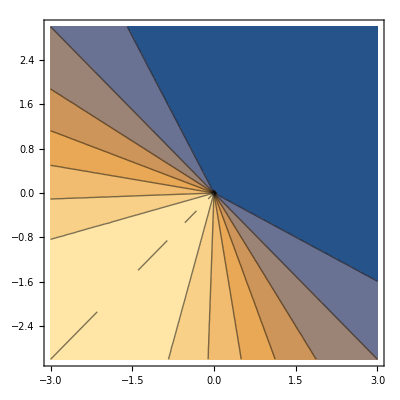
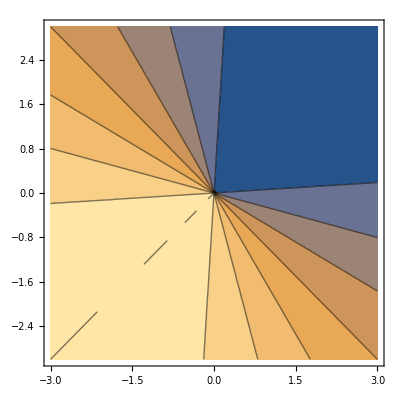
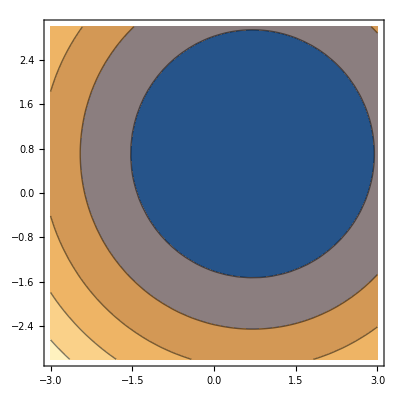
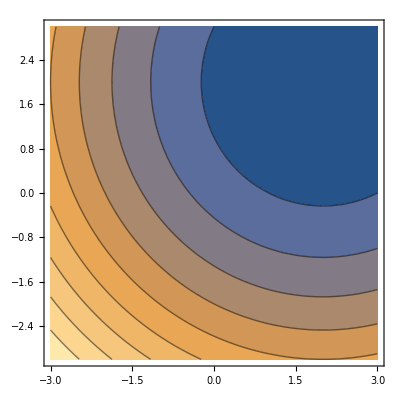
Shape | Normalized Least Squares | LS To Normalize Target | LS
-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*We should be able to see the asymptotic behavior of these two objective functions by comparing the distance of a fixed vector to an arbitrary vector.*)
Module[{siz=400,dis=3.,
vec={2,2}
},
P3=Plot3D[#/.{b1->vec⟦1⟧,b2->vec⟦2⟧},{a1,-dis,dis},{a2,-dis,dis},ImageSize->siz,PlotTheme->"Web"]&;
C3=ContourPlot[#/.{b1->vec⟦1⟧,b2->vec⟦2⟧},{a1,-dis,dis},{a2,-dis,dis},ImageSize->siz]&;
Target={S1,N1,HN1,LS1};
Quiet@Grid[
{{"Shape","Normalized Least Squares","LS To Normalize Target", "LS"},
P3/@Target,C3/@Target},
Frame->All]
]
(*VEC here is the arbitrarily picked example vector.
The objective function surface merely rotates as VEC changes angle.
The surface does not change as VEC's magnitude changes.*)
```